```mathematica
Clear["Global`*"]
```

### Calculating displacements correlation for 2 connected particles in 1D

```mathematica
A=ω0({{-1, 0, 1, 0}, {0, -1, 0, 1}, {1, 0, -1, 0}, {0, 1, 0, -1}});
eigsys=Eigensystem[A];
U = eigsys[[2]];
U//MatrixForm
λs=eigsys[[1]]
Um1=Inverse[U];
(*λ=-2 k12/γ;*)
b[1]={√(2 D1),0,0,0};
b[2]={0, √(2D1),0,0};
b[3]={0, 0,√(2D2),0};
b[4]={0, 0,0,√(2D2)};
R0={R01,R02,R03,R04};
```

(0 | -1 | 0 | 1
-1 | 0 | 1 | 0
0 | 1 | 0 | 1
1 | 0 | 1 | 0)

{-2 ω0,-2 ω0,0,0}

```mathematica
Map[J[Δt (n+1),#]&,λs]
```

{J[(1+n) Δt,-2 ω0],J[(1+n) Δt,-2 ω0],J[(1+n) Δt,0],J[(1+n) Δt,0]}

```mathematica
Map[J[#]&,λs]
```

{J[-2 ω0],J[-2 ω0],J[0],J[0]}

J is the integral of the exponent Exp[A(-s)] over the stochastic process from time 0 to the indicated time

```mathematica
dRn=U.(DiagonalMatrix[Exp[λs Δt (n+1)]]-DiagonalMatrix[Exp[λs Δt n]]).Um1.R0 +Sum[p[i] U.DiagonalMatrix[Map[J[Δt (n+1),#]&,λs]].Um1.b[i],{i,1,4}]-Sum[p[i] U.DiagonalMatrix[Map[J[Δt n,#]&,λs]].Um1.b[i],{i,1,4}];
dRn//MatrixForm
```

(1/2 (-ⅇ^(-2 n Δt ω0)+ⅇ^(-2 (1+n) Δt ω0)) R01+1/2 (ⅇ^(-2 n Δt ω0)-ⅇ^(-2 (1+n) Δt ω0)) R03-√2 √D1 (1/2 J[n Δt,0]+1/2 J[n Δt,-2 ω0]) p[1]+√2 √D1 (1/2 J[(1+n) Δt,0]+1/2 J[(1+n) Δt,-2 ω0]) p[1]-√2 √D2 (1/2 J[n Δt,0]-1/2 J[n Δt,-2 ω0]) p[3]+√2 √D2 (1/2 J[(1+n) Δt,0]-1/2 J[(1+n) Δt,-2 ω0]) p[3]
1/2 (-ⅇ^(-2 n Δt ω0)+ⅇ^(-2 (1+n) Δt ω0)) R02+1/2 (ⅇ^(-2 n Δt ω0)-ⅇ^(-2 (1+n) Δt ω0)) R04-√2 √D1 (1/2 J[n Δt,0]+1/2 J[n Δt,-2 ω0]) p[2]+√2 √D1 (1/2 J[(1+n) Δt,0]+1/2 J[(1+n) Δt,-2 ω0]) p[2]-√2 √D2 (1/2 J[n Δt,0]-1/2 J[n Δt,-2 ω0]) p[4]+√2 √D2 (1/2 J[(1+n) Δt,0]-1/2 J[(1+n) Δt,-2 ω0]) p[4]
1/2 (ⅇ^(-2 n Δt ω0)-ⅇ^(-2 (1+n) Δt ω0)) R01+1/2 (-ⅇ^(-2 n Δt ω0)+ⅇ^(-2 (1+n) Δt ω0)) R03-√2 √D1 (1/2 J[n Δt,0]-1/2 J[n Δt,-2 ω0]) p[1]+√2 √D1 (1/2 J[(1+n) Δt,0]-1/2 J[(1+n) Δt,-2 ω0]) p[1]-√2 √D2 (1/2 J[n Δt,0]+1/2 J[n Δt,-2 ω0]) p[3]+√2 √D2 (1/2 J[(1+n) Δt,0]+1/2 J[(1+n) Δt,-2 ω0]) p[3]
1/2 (ⅇ^(-2 n Δt ω0)-ⅇ^(-2 (1+n) Δt ω0)) R02+1/2 (-ⅇ^(-2 n Δt ω0)+ⅇ^(-2 (1+n) Δt ω0)) R04-√2 √D1 (1/2 J[n Δt,0]-1/2 J[n Δt,-2 ω0]) p[2]+√2 √D1 (1/2 J[(1+n) Δt,0]-1/2 J[(1+n) Δt,-2 ω0]) p[2]-√2 √D2 (1/2 J[n Δt,0]+1/2 J[n Δt,-2 ω0]) p[4]+√2 √D2 (1/2 J[(1+n) Δt,0]+1/2 J[(1+n) Δt,-2 ω0]) p[4])

### Covariance matrix for any lag

```mathematica
covMat = Transpose[{dRn}].{dRn/.n->n+j};
rulesP={p[_]^2:>1,p[i_] p[j_] :> 0/;i≠j};
rulesP2={p[_]:>0};
corRule=J[t1_,λ1_]J[t2_,λ2_]:>Exp[λ1 t1 + λ2 t2]If[λ1!=0||λ2!=0,(1-Exp[-(λ1+λ2)*Min[{t1,t2}]])/(λ1+λ2),Min[{t1,t2}]];
corRule2=J[t1_,λ_]:>0;
covMat2=((covMat//ExpandAll)/.rulesP)/.rulesP2;
covMatLag0=Simplify[covMat2/.corRule/.corRule2,Assumptions->{n>=0,Δt>0,j==0,ω0≠0}];
covMatLagNot0=Simplify[covMat2/.corRule/.corRule2,Assumptions->{n>=0,Δt>0,j≥1,ω0≠0}];
```

```mathematica
covMatLag0[[1,1]]//MatrixForm
covMatLagNot0[[1,1]]//MatrixForm
```

1/(8 ω0)ⅇ^(-2 (4+5 n) Δt ω0) (4 (D1-D2) ⅇ^(2 (3+5 n) Δt ω0) (-1+ⅇ^(2 Δt ω0))+4 (D1+D2) ⅇ^(2 (4+5 n) Δt ω0) Δt ω0-2 ⅇ^(6 (1+n) Δt ω0) (D1 (-1+ⅇ^(4 n Δt ω0))+D2 (-1+ⅇ^(4 n Δt ω0))+2 (R01-R03)^2 ω0)+ⅇ^(2 (4+3 n) Δt ω0) (D1 (-1+ⅇ^(4 n Δt ω0))+D2 (-1+ⅇ^(4 n Δt ω0))+2 (R01-R03)^2 ω0)+ⅇ^(2 (2+3 n) Δt ω0) (D1 (-1+ⅇ^(4 (1+n) Δt ω0))+D2 (-1+ⅇ^(4 (1+n) Δt ω0))+2 (R01-R03)^2 ω0))

-(ⅇ^(-2 (2+j+2 n) Δt ω0) (-1+ⅇ^(2 Δt ω0))^2 (D1+D2+3 D1 ⅇ^(2 (1+2 n) Δt ω0)-D2 ⅇ^(2 (1+2 n) Δt ω0)-2 (R01-R03)^2 ω0))/(8 ω0)

### Tests

```mathematica
s1=Simplify[covMat2[[1,1]]/.corRule/.corRule2,Assumptions->{n≥0,Δt>0,ω0>0,j≥0}]
Collect[Simplify[Refine[s1,j≥1]],{D1, D2}]/.{R01->0,R03->0}
Collect[Simplify[s1/.j->0],{D1, D2}]/.{R01->0,R03->0}
```

Piecewise[{{-(ⅇ^(-2 (2+j+2 n) Δt ω0) (-1+ⅇ^(2 Δt ω0))^2 (D1+D2+3 D1 ⅇ^(2 (1+2 n) Δt ω0)-D2 ⅇ^(2 (1+2 n) Δt ω0)-2 (R01-R03)^2 ω0))/(8 ω0), j≥1}, {1/(8 ω0)ⅇ^(-2 (2+j+2 n) Δt ω0) (2 (-1+ⅇ^(2 Δt ω0))^2 (R01-R03)^2 ω0+D2 (-1+2 ⅇ^(2 Δt ω0)-ⅇ^(4 Δt ω0)-2 ⅇ^(4 (1+n) Δt ω0)+ⅇ^(2 (1+2 n) Δt ω0)+ⅇ^(2 (Δt+2 (j+n) Δt) ω0)-4 ⅇ^(2 (2+j+2 n) Δt ω0) (-1+j) Δt ω0)-D1 (1-2 ⅇ^(2 Δt ω0)+ⅇ^(4 Δt ω0)-6 ⅇ^(4 (1+n) Δt ω0)+3 ⅇ^(2 (1+2 n) Δt ω0)+3 ⅇ^(2 (Δt+2 (j+n) Δt) ω0)+4 ⅇ^(2 (2+j+2 n) Δt ω0) (-1+j) Δt ω0)), True}}]

-(D2 ⅇ^(-2 (2+j+2 n) Δt ω0) (-1+ⅇ^(2 Δt ω0))^2 (1-ⅇ^(2 (1+2 n) Δt ω0)))/(8 ω0)-(D1 ⅇ^(-2 (2+j+2 n) Δt ω0) (-1+ⅇ^(2 Δt ω0))^2 (1+3 ⅇ^(2 (1+2 n) Δt ω0)))/(8 ω0)

(D2 ⅇ^(-4 (1+n) Δt ω0) (-1+2 ⅇ^(2 Δt ω0)-ⅇ^(4 Δt ω0)+2 ⅇ^(2 (1+2 n) Δt ω0)-ⅇ^(4 (1+n) Δt ω0) (2-4 Δt ω0)))/(8 ω0)+(D1 ⅇ^(-4 (1+n) Δt ω0) (-1+2 ⅇ^(2 Δt ω0)-ⅇ^(4 Δt ω0)-6 ⅇ^(2 (1+2 n) Δt ω0)+2 ⅇ^(4 (1+n) Δt ω0) (3+2 Δt ω0)))/(8 ω0)

### Check if no interactions

```mathematica
Limit[covMatLag0, ω0->0]
 Limit[covMatLagNot0, ω0->0]
```

{{2 D1 Δt,0,0,0},{0,2 D1 Δt,0,0},{0,0,2 D2 Δt,0},{0,0,0,2 D2 Δt}}

{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}

### Take the time average ω0 = k12/γ

```mathematica
covMatLag0TimeAverage = Limit[Simplify[Sum[covMatLag0/M,{n,0, M-1}]],M->∞,Assumptions->{Δt >0,ω0>0}];
covMatLag0TimeAverage//MatrixForm
covMatLagNot0TimeAverage = Collect[Limit[Sum[covMatLagNot0/M,{n,0, M}],M->∞,Assumptions->{ω0>0,Δt>0}],{D1,D2}];
covMatLagNot0TimeAverage//MatrixForm
```

((D1 (3-3 ⅇ^(-2 Δt ω0)+2 Δt ω0)+D2 (-1+ⅇ^(-2 Δt ω0)+2 Δt ω0))/(4 ω0) | 0 | ((D1+D2) ⅇ^(-2 Δt ω0) (1+ⅇ^(2 Δt ω0) (-1+2 Δt ω0)))/(4 ω0) | 0
0 | (D1 (3-3 ⅇ^(-2 Δt ω0)+2 Δt ω0)+D2 (-1+ⅇ^(-2 Δt ω0)+2 Δt ω0))/(4 ω0) | 0 | ((D1+D2) ⅇ^(-2 Δt ω0) (1+ⅇ^(2 Δt ω0) (-1+2 Δt ω0)))/(4 ω0)
((D1+D2) ⅇ^(-2 Δt ω0) (1+ⅇ^(2 Δt ω0) (-1+2 Δt ω0)))/(4 ω0) | 0 | -(D1-3 D2-D1 ⅇ^(-2 Δt ω0)+3 D2 ⅇ^(-2 Δt ω0)-2 D1 Δt ω0-2 D2 Δt ω0)/(4 ω0) | 0
0 | ((D1+D2) ⅇ^(-2 Δt ω0) (1+ⅇ^(2 Δt ω0) (-1+2 Δt ω0)))/(4 ω0) | 0 | -(D1-3 D2-D1 ⅇ^(-2 Δt ω0)+3 D2 ⅇ^(-2 Δt ω0)-2 D1 Δt ω0-2 D2 Δt ω0)/(4 ω0))

(-(3 D1 ⅇ^(-2 (1+j) Δt ω0) (-1+ⅇ^(2 Δt ω0))^2)/(8 ω0)+(D2 ⅇ^(-2 (1+j) Δt ω0) (-1+ⅇ^(2 Δt ω0))^2)/(8 ω0) | 0 | (3 D1 ⅇ^(-2 (1+j) Δt ω0) (-1+ⅇ^(2 Δt ω0))^2)/(8 ω0)-(D2 ⅇ^(-2 (1+j) Δt ω0) (-1+ⅇ^(2 Δt ω0))^2)/(8 ω0) | 0
0 | -(3 D1 ⅇ^(-2 (1+j) Δt ω0) (-1+ⅇ^(2 Δt ω0))^2)/(8 ω0)+(D2 ⅇ^(-2 (1+j) Δt ω0) (-1+ⅇ^(2 Δt ω0))^2)/(8 ω0) | 0 | (3 D1 ⅇ^(-2 (1+j) Δt ω0) (-1+ⅇ^(2 Δt ω0))^2)/(8 ω0)-(D2 ⅇ^(-2 (1+j) Δt ω0) (-1+ⅇ^(2 Δt ω0))^2)/(8 ω0)
-(D1 ⅇ^(-2 (1+j) Δt ω0) (-1+ⅇ^(2 Δt ω0))^2)/(8 ω0)+(3 D2 ⅇ^(-2 (1+j) Δt ω0) (-1+ⅇ^(2 Δt ω0))^2)/(8 ω0) | 0 | (D1 ⅇ^(-2 (1+j) Δt ω0) (-1+ⅇ^(2 Δt ω0))^2)/(8 ω0)-(3 D2 ⅇ^(-2 (1+j) Δt ω0) (-1+ⅇ^(2 Δt ω0))^2)/(8 ω0) | 0
0 | -(D1 ⅇ^(-2 (1+j) Δt ω0) (-1+ⅇ^(2 Δt ω0))^2)/(8 ω0)+(3 D2 ⅇ^(-2 (1+j) Δt ω0) (-1+ⅇ^(2 Δt ω0))^2)/(8 ω0) | 0 | (D1 ⅇ^(-2 (1+j) Δt ω0) (-1+ⅇ^(2 Δt ω0))^2)/(8 ω0)-(3 D2 ⅇ^(-2 (1+j) Δt ω0) (-1+ⅇ^(2 Δt ω0))^2)/(8 ω0))

### Take the time average in the finite-time limit

```mathematica
Clear[M0];
covMatLag0TimeAverageFinite = Simplify[Sum[covMatLag0/M0,{n,0, M0-1}]];
covMatLag0TimeAverageFinite//MatrixForm;
covMatLagNot0TimeAverageFinite = Sum[covMatLagNot0/M0,{n,0, M0}];
covMatLagNot0TimeAverageFinite//MatrixForm;
```

### Check if one particle can go unnoticed

```mathematica
covMatLag0TimeAverage[[1,1]]
Series[%,{Δt,0,2}]
covMatLagNot0TimeAverage[[1,1]]
Series[%,{Δt,0,2}]
```

(D1 (3-3 ⅇ^(-2 Δt ω0)+2 Δt ω0)+D2 (-1+ⅇ^(-2 Δt ω0)+2 Δt ω0))/(4 ω0)

2 D1 Δt+1/2 (-3 D1 ω0+D2 ω0) Δt^2+O[Δt]^3

-(3 D1 ⅇ^(-2 (1+j) Δt ω0) (-1+ⅇ^(2 Δt ω0))^2)/(8 ω0)+(D2 ⅇ^(-2 (1+j) Δt ω0) (-1+ⅇ^(2 Δt ω0))^2)/(8 ω0)

1/2 (-3 D1 ω0+D2 ω0) Δt^2+O[Δt]^3

```mathematica
covMatLag0TimeAverage[[1;;2,1;;2]]/.D2->3 D1//Simplify//MatrixForm
```

(2 D1 Δt | 0
0 | 2 D1 Δt)

```mathematica
covMatLagNot0TimeAverage[[1;;2,1;;2]]/.D2->3D1//Simplify//MatrixForm
```

(0 | 0
0 | 0)

### Check whether for j = 0, the lag matrix gives the same as for j != 0

```mathematica
(covMat1Lag0[[1;;2,1;;2]]-(covMat1LagNot0[[1;;2,1;;2]]/.j->0)-DiagonalMatrix[{2 D1 Δt,2 D2 Δt}])//FullSimplify
```

Part::take: Cannot take positions 1 through 2 in covMat1Lag0.

Part::take: Cannot take positions 1 through 2 in covMat1LagNot0.

{{-2 D1 Δt+covMat1Lag0⟦1;;2,1;;2⟧-covMat1LagNot0⟦1;;2,1;;2⟧,covMat1Lag0⟦1;;2,1;;2⟧-covMat1LagNot0⟦1;;2,1;;2⟧},{covMat1Lag0⟦1;;2,1;;2⟧-covMat1LagNot0⟦1;;2,1;;2⟧,-2 D2 Δt+covMat1Lag0⟦1;;2,1;;2⟧-covMat1LagNot0⟦1;;2,1;;2⟧}}

### Extract only the properties of particle 1

```mathematica
covMat1Lag0=covMatLag0TimeAverage[[1;;2,1;;2]];
%//MatrixForm
covMat1Lag0[[1,1]]==covMat1Lag0[[2,2]]
covMat1LagNot0=covMatLagNot0TimeAverage[[1;;2,1;;2]];
%//MatrixForm
covMat1LagNot0[[1,1]]==covMat1LagNot0[[2,2]]
```

((D1 (3-3 ⅇ^(-2 Δt ω0)+2 Δt ω0)+D2 (-1+ⅇ^(-2 Δt ω0)+2 Δt ω0))/(4 ω0) | 0
0 | (D1 (3-3 ⅇ^(-2 Δt ω0)+2 Δt ω0)+D2 (-1+ⅇ^(-2 Δt ω0)+2 Δt ω0))/(4 ω0))

True

(-(3 D1 ⅇ^(-2 (1+j) Δt ω0) (-1+ⅇ^(2 Δt ω0))^2)/(8 ω0)+(D2 ⅇ^(-2 (1+j) Δt ω0) (-1+ⅇ^(2 Δt ω0))^2)/(8 ω0) | 0
0 | -(3 D1 ⅇ^(-2 (1+j) Δt ω0) (-1+ⅇ^(2 Δt ω0))^2)/(8 ω0)+(D2 ⅇ^(-2 (1+j) Δt ω0) (-1+ⅇ^(2 Δt ω0))^2)/(8 ω0))

True

### The autocorrelation below is already averaged over time (divided by time T)

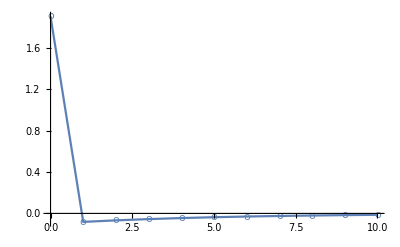

-Graphics-

```mathematica
dxAutocorr1[j1_]:=If[j1==0, covMatLag0TimeAverage[[1,1]],covMatLagNot0TimeAverage[[1,1]]/.j->j1];
(*dxAutocorr1[j1_]:=If[j1==0, 2D1 Δt,0];*)
rulesValues = {D2->1D1,Δt->1 10^-1,ω0->1 10^0};
dxDiscrete=Table[{j,dxAutocorr1[j]/(D1  Δt)},{j,0,10}];
ListPlot[dxDiscrete/.rulesValues,Joined->True,AxesOrigin->{0,0},PlotMarkers->"o", PlotRange->All]
dxDiscrete[[1;;2]]//FullSimplify;

M0=100;df = 1/(Δt M0);
s2=Table[dxAutocorr1[j],{j,0,M0}];
A=Δt  Fourier[s2/.rulesValues/.D1->1,FourierParameters->{1, -1}];(* power spectrum *)

(*A=Abs[s3]^2 df /.rulesValues;*)
P=A /Δt^2/.rulesValues;
s4 = Table[{j,Re[P[[j+1]]]},{j,0,M0}]/.rulesValues;
ListPlot[s4,PlotRange->{All,{0,All}},Joined->True,AxesOrigin->{0,0},PlotMarkers->"o"]
```

```mathematica
Fourier[Table[1,{j,1,10}],FourierParameters->{1, -1}]
```

{10.,0.,4.44089×10^-16,0.,4.44089×10^-16,0.,4.44089×10^-16,0.,4.44089×10^-16,0.}

```mathematica
s3
```

s3

### Calculate the exact discrete Fourier transform of the time-averaged auto-correlation.

```mathematica
covMatrixParticle1[j1_]:=If[j1==0,covMat1Lag0,covMat1LagNot0/.j->j1];
Clear[M0];
covMat1LagNot0 Exp[-2 π ⅈ/M0 k j]//Simplify;
t1=covMat1Lag0+Sum[covMat1LagNot0 Exp[-2 π ⅈ/M0 k j],{j,1,M0-1}];
powerSpectrum = Δt  t1
Limit[powerSpectrum,M0->∞,Assumptions->{k>=0,ω0>0,Δt>0}]
```

{{Δt (((3 D1-D2) ⅇ^(-2 ⅈ k π-2 Δt ω0-2 (1+M0) Δt ω0) (-1+ⅇ^(2 Δt ω0))^2 (ⅇ^((2 ⅈ k π)/M0+4 Δt ω0)-ⅇ^(2 ⅈ k π+2 (1+M0) Δt ω0)))/(8 (-1+ⅇ^((2 ⅈ k π)/M0+2 Δt ω0)) ω0)+(D1 (3-3 ⅇ^(-2 Δt ω0)+2 Δt ω0)+D2 (-1+ⅇ^(-2 Δt ω0)+2 Δt ω0))/(4 ω0)),0},{0,Δt (((3 D1-D2) ⅇ^(-2 ⅈ k π-2 Δt ω0-2 (1+M0) Δt ω0) (-1+ⅇ^(2 Δt ω0))^2 (ⅇ^((2 ⅈ k π)/M0+4 Δt ω0)-ⅇ^(2 ⅈ k π+2 (1+M0) Δt ω0)))/(8 (-1+ⅇ^((2 ⅈ k π)/M0+2 Δt ω0)) ω0)+(D1 (3-3 ⅇ^(-2 Δt ω0)+2 Δt ω0)+D2 (-1+ⅇ^(-2 Δt ω0)+2 Δt ω0))/(4 ω0))}}

{{(ⅇ^(-2 Δt ω0) Δt (D2+D2 ⅇ^(2 Δt ω0) (-1+4 Δt ω0)+D1 (-3+ⅇ^(2 Δt ω0) (3+4 Δt ω0))))/(8 ω0),0},{0,(ⅇ^(-2 Δt ω0) Δt (D2+D2 ⅇ^(2 Δt ω0) (-1+4 Δt ω0)+D1 (-3+ⅇ^(2 Δt ω0) (3+4 Δt ω0))))/(8 ω0)}}

### Plot the theoretical power spectrum normalized to Δt^2 of the first particle

```mathematica
M0=20;
rulesValues = {D2->1D1,Δt->1 10^-1,ω0->1 10^-0};
q1 = Simplify[Table[{k,N[Re[powerSpectrum[[1,1]]/(D1 Δt^2)]]},{k,0,M0}]/.rulesValues,Assumptions->D1>0];
ListPlot[q1,PlotRange->{All,{0,All}},Joined->True,AxesOrigin->{0,0},PlotMarkers->"o"]
```

-Graphics-

```mathematica
covMatrixParticle1[j1]Exp[-2 π ⅈ/M0 k j1]
```

ⅇ^(-1/10 ⅈ j1 k π) If[j1==0,covMat1Lag0,covMat1LagNot0/.j→j1]

```mathematica
Eigensystem[ω0({{-1, 0, 1, 0}, {0, 0, 0, 0}, {1, 0, -1, 0}, {0, 0, 0, 0}})]
%[[2]]//MatrixForm
Inverse[%]
```

{{-2 ω0,0,0,0},{{-1,0,1,0},{0,0,0,1},{1,0,1,0},{0,1,0,0}}}

(-1 | 0 | 1 | 0
0 | 0 | 0 | 1
1 | 0 | 1 | 0
0 | 1 | 0 | 0)

{{-1/2,0,1/2,0},{0,0,0,1},{1/2,0,1/2,0},{0,1,0,0}}

```mathematica
Integrate[Exp[-ξ1^2/(2 σ1^2)-(η-ξ1)^2/(2 σ2^2)],{ξ1,-∞,∞},Assumptions->{σ1>0,σ2>0}]
```

(ⅇ^(-η^2/(2 (σ1^2+σ2^2))) √(2 π) σ1 σ2)/(√(σ1^2+σ2^2))

```mathematica
Sum[Cos[(2π k n)/M]^2,{n, 0, M-1},Assumptions->{k∈Integers,M∈Integers}]
```

1/4 (1+2 M+Csc[(2 k π)/M] Sin[(2 (-k π+2 k M π))/M])

```mathematica
Csc[0]
```

ComplexInfinity